# Homework 5 Section 3.1

#### 1) Taylor Expansion

```mathematica
f[x_] := x*Exp[-x]-1;
```

```mathematica
f[x]
```

-1+ⅇ^-x x

```mathematica
d[x] = D[f[x],x]
```

ⅇ^-x-ⅇ^-x x

```mathematica
g[x] = f[2.5]
```

-0.794788

```mathematica
For[i=1,i≤3,i++,
d[x] = D[f[x], {x,i}];
g[x] = g[x] + (1/i!)*(d[x] /. x-> 2.5)*(x-2.5)^i;
];
```

```mathematica
g[x]
```

-0.794788-0.123127 (-2.5+x)+0.0205212 (-2.5+x)^2+0.00684042 (-2.5+x)^3

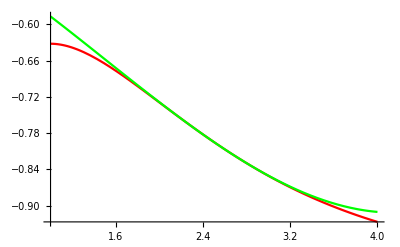

```mathematica
Plot[{f[x],g[x]}, {x,1,4},PlotStyle->{Red,Green}]
```

```mathematica
h[x_] := (f[x] - g[x])^2
```

```mathematica
normerror = (Integrate[h[x],{x,1,4}])^0.5
```

0.0187681

```mathematica
meannormerror = (1/3)*(Integrate[h[x],{x,1,4}])^0.5
```

0.00625605

#### 2) Polynomial Interpolation

```mathematica
f[x_] := x*Exp[-x]-1;
```

```mathematica
mymatrix = {};
For[i=1,i≤4,i++,
rows = {};
For[j=0,j≤3,j++,
AppendTo[rows,(Subscript[x, i])^j]];
AppendTo[mymatrix,rows]];
```

```mathematica
mymatrix
```

{{1,x_1,x_1^2,x_1^3},{1,x_2,x_2^2,x_2^3},{1,x_3,x_3^2,x_3^3},{1,x_4,x_4^2,x_4^3}}

```mathematica
Subscript[x, 1] = 1;
Subscript[x, 2] = 2;
Subscript[x, 3] = 3;
Subscript[x, 4] = 4;
```

```mathematica
c = {{f[1],f[2],f[3],f[4]}}
```

{{-1+1/ⅇ,-1+2/ⅇ^2,-1+3/ⅇ^3,-1+4/ⅇ^4}}

```mathematica
c=Transpose[c]
```

{{-1+1/ⅇ},{-1+2/ⅇ^2},{-1+3/ⅇ^3},{-1+4/ⅇ^4}}

```mathematica
d =LinearSolve[mymatrix,N[c,10]]
```

{{-0.6283233693},{0.06601238588},{-0.08136144183},{0.01155186642}}

```mathematica
P[x_] := d[[1]]+d[[2]]*x+d[[3]]x^2+d[[4]]x^3
```

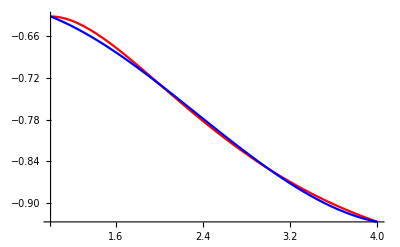

```mathematica
Plot[{f[x],P[x]},{x,1,4},PlotStyle->{Red,Blue}]
```

```mathematica
h[x_] := (f[x] - P[x])^2
```

```mathematica
h[x]
```

{(-0.371676631-0.06601238588 x+ⅇ^-x x+0.08136144183 x^2-0.01155186642 x^3)^2}

```mathematica
normerror = (Integrate[h[x],{x,1,4}])^0.5
```

{0.502137}

```mathematica
meannormerror = (1/3)*(Integrate[h[x],{x,1,4}])^0.5
```

{0.167379}

According to the norm error and mean norm error, the Taylor expansion is better than p, although graphically, p looks better.

Maximum Absolute error

```mathematica
Maximize[{D[f[x],x,x,x,x],1≤x≤4},x]
```

{0,{x→4}}

```mathematica
answer[x_] = D[f[x],x,x,x,x]
```

-4 ⅇ^-x+ⅇ^-x x

```mathematica
m[x] =(answer[x]*(4-1)^4) / 4!
```

27/8 (-4 ⅇ^-x+ⅇ^-x x)

```mathematica
(** x=1 **)
```

```mathematica
N[m[x]/. x->1,5]
```

-3.7248

```mathematica
(** x= 2 **)
```

```mathematica
N[m[x]/. x->2,5]
```

-0.91351

```mathematica
(** x = 3 **)
```

```mathematica
N[m[x]/. x->3,5]
```

-0.16803

```mathematica
(** x = 4 **)
```

```mathematica
N[m[x]/. x->4,5]
```

0

#### 7)

```mathematica
f[x_] := 1 / (1+x^2);
thirderivative[x] = D[f[x],x,x,x]
mew = Maximize[{thirderivative[x],-4≤x≤4},x]
```

-(48 x^3)/((1+x^2)^4)+(24 x)/((1+x^2)^3)

{-(24 (-√(1/5 (5-2 √5))+(5-2 √5)^(3/2)/(5 √5)))/(1+1/5 (5-2 √5))^4,{x→√(1/5 (5-2 √5))}}

```mathematica
N[√(1/5 (5-2 √5)),10]
```

0.3249196962

```mathematica
Subscript[a, 0] = 0.2;
For[i=1,i<40,i++,
Subscript[a, i]=Subscript[a, i-1]+0.2]
```

```mathematica
newmatrix = {};
b=1;
For[i=b,i≤b+2,i++,
row = {};
For[j=0,j≤2,j++,
Which[i==b+1,
AppendTo[row,((Subscript[a, i-1]+Subscript[a, i])/2)^j],
i==b,
AppendTo[row,(Subscript[a, b])^j],
i==b+2,
AppendTo[row,(Subscript[a, i-1])^j]]];
AppendTo[newmatrix,row]]
```

```mathematica
(** This loop will provide 3 subintervals. Just change b, where b can take values from 0 to 37, which constitutes the 40 subintervals required. I chose b = 2 because the graph crosses f(x) at b=2 **)
```

```mathematica
newmatrix
```

{{1.,0.4,0.16},{1.,0.5,0.25},{1.,0.6,0.36}}

```mathematica
c = {{f[0.2],f[0.4],f[0.6]}};
c= Transpose[c]
```

{{0.961538},{0.862069},{0.735294}}

```mathematica
d = LinearSolve[newmatrix,N[c,10]]
```

{{1.08636},{0.234046},{-1.36527}}

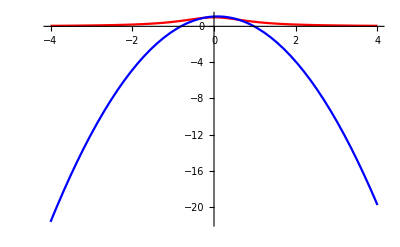

```mathematica
R[x_]:= d[[1]]+d[[2]]*x+d[[3]]*x^2;
Plot[{f[x],R[x]},{x,-4,4},PlotStyle->{Red,Blue}]
```

```mathematica
mew
```

{-(24 (-√(1/5 (5-2 √5))+(5-2 √5)^(3/2)/(5 √5)))/(1+1/5 (5-2 √5))^4,{x→√(1/5 (5-2 √5))}}

```mathematica
value =N[mew[[1]],10]
```

4.668559284

```mathematica
errorbound = (value * 8^3)/3!
```

398.3837256

```mathematica
value / (6*(0.2)^40)
```

7.07672×10^27

#### Extra Credit

I will use the exponential growth/ decay formula that is popular in algebra courses

```mathematica
f[t_] :=  P*Exp[r*t];
```

```mathematica
(** To make computation easier, I will assign values for P and r **)
P = 10000;
r = 0.2;
```

```mathematica
mymatrix = {};
For[i=1,i≤10,i++,
rows = {};
For[j=0,j≤9,j++,
If[i<6,
AppendTo[rows,(Subscript[t, -i])^j],
AppendTo[rows,(Subscript[t, i-5])^j];]];
AppendTo[mymatrix,rows]];
```

```mathematica
For[i=1,i≤10,i++,
If[i<6,
Subscript[t, -i]=-i,
Subscript[t, i-5]=i-5]]
```

```mathematica
c = {{f[-5],f[-4],f[-3],f[-2],f[-1],f[0],f[1],f[2],f[3],f[4]}};
c=Transpose[c]
```

{{3678.79},{4493.29},{5488.12},{6703.2},{8187.31},{10000.},{12214.},{14918.2},{18221.2},{22255.4}}

```mathematica
d =LinearSolve[mymatrix,c]
```

{{6218.86},{3887.62},{655.933},{-826.182},{-37.1353},{104.549},{1.76455},{-5.47947},{-0.0300988},{0.098425}}

```mathematica
jet[t_] := d[[1]]+d[[2]]t+d[[3]] t^2+d[[4]] t^3+d[[5]] t^4+d[[6]] t^5+
d[[7]] t^6+d[[8]] t^7+d[[9]] t^8+d[[10]] t^9;
```

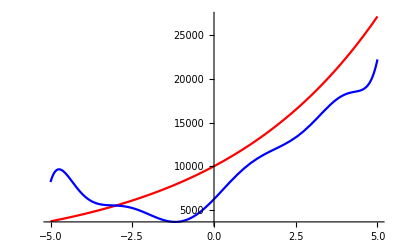

```mathematica
Plot[{f[t],jet[t]}, {t,-5,5}, PlotStyle->{Red,Blue}]
```

```mathematica
h[t_] := (f[t] - jet[t])^2
```

```mathematica
normerror = (Integrate[h[t],{t,-5,4}])^0.5
```

{9562.93}

```mathematica
meannormerror = (1/9)*(Integrate[h[t],{x,-5,4}])^0.5
```

{0.333333 ((-6218.86+10000 ⅇ^(0.2 t)-3887.62 t-655.933 t^2+826.182 t^3+37.1353 t^4-104.549 t^5-1.76455 t^6+5.47947 t^7+0.0300988 t^8-0.098425 t^9)^2)^0.5}

```mathematica
tenth[t] = D[f[t],{t,10}]
```

0.001024 ⅇ^(0.2 t)

```mathematica
mew = Maximize[{tenth[t],-4≤t≤4},t]
```

{0.00227895,{t→4.}}

```mathematica
bound = mew[[1]]
```

0.00227895

```mathematica
(** error bound below **)
```

```mathematica
errorbound = (bound*(9)^10)/10!
```

2.18977

The derivative of the interpolation does not approximate the derivative of my function well. There are pretty big errors and the graph is a little off from the original function.